# Graduate Algorithms Week 7: Part 2

# Planar Graphs and Graph Coloring

## The Art of Graph Coloring: Another Example

### Section 6.1. Graph coloring as an aesthetic euphemism for scheduling.

Motivation. Suppose Crayola Airlines of Aspen Colorado wishes to run seven flights every week, all originating in Aspen as shown below.

Flight		Route

A		     Burley → Twin Falls → Boise → Lewiston	
B		     Billings → Great Falls → Missoula → Lewiston
C		     Idaho Falls → Boise → Lewiston → Pullman
D		     Idaho Falls → Yellowstone → Great Falls
E		     Idaho Falls → Sun Valley → Boise
F		     Butte → Missoula → Lewiston
G		     Butte → Helena → Great Falls

Scheduling Contraints.

Flights only occur on Monday, Wednesday, and Friday, and

no more than one flight per day can visit any given town.

## Graph Coloring

### Big Question:

Is such a schedule possible? How can we tell?

### One Possible Method:

Let’s model the problem by creating a simple graph H with one vertex representing each route.

Join two vertices in H by an edge if and only if the two correponding routes share a town.

For example vertices C and D are neighbors in graph H because routes C and D both go to Idaho Falls.

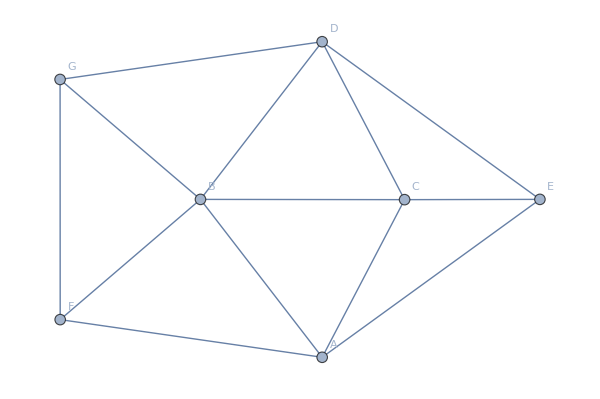

## Crayola Airlines Scheduling Problem, continued

If there is a solution to the scheduling problem then we should be able to assign labels Monday, Wednesday, and Friday to the vertices of H so that not two vertices with the same label are joined by an edge (an edge represents a scheduling conflict).

For convenience, let Monday = R, Wednesday = G, and Friday = B.

Can we “3-color” the graph H???

-Graphics-

## Definitions

### Definition 6.1 [k-coloring, proper k-coloring, color class, chromatic number]

A k-coloring of a graph G is a labeling f: V(G) → S, where S = {1,2,…,k} and the function f is onto S. The labels are called colors; the vertices of one color form a color class.

A k-coloring is called proper if adjacent vertices have distinct labels. A graph is k-colorable if it has a proper k-coloring.

The chromatic number of a graph G, written χ(G), is the smallest k such that G is properly k-colorable.

## Some Facts about the Chromatic Number Function

If |V(G)| = n, then χ(G) ≤ n.

If H < G then  χ(H) ≤ χ(G).

χ(K_n) = n ∀ n ≥ 1.

If K_n < G, then χ(G) ≥ n.

If G has connected components G_1, G_2, …, G_r, then χ(G) = max_(1≤i≤r) {χ(G_i)}.

## Map Coloring in the plane and the Four Color Theorem

Motivation. What is the minimum number of colors needed to color the states of the U.S. so that every two states that share a common border receive different colors?

Note. If two states share only a common point (as opposed to a piece of a Jordan Curve) then they are allowed to be labeled with the same color.

## Correspondence between maps drawn in the plane and planar graphs

Given a cartographers map M, we assume that each country (or state or territory or ...) is a connected region.

With each such map there is an associated graph G called the dual of M

The vertices of G correspond to the regions of M; two vertices are adjacent if and only if the corresponding regions share a non-trivial border (i.e., more than just a point).

Fact: The dual of a cartographers map is a planar graph.

## Big Problem

What is the largest chromatic number of any planar map/graph?

## If G is planar how big can χ(G) be?

### Theorem 6.3 [The 6-color theorem for planar graphs]

Let G be a planar graph. Then χ(G) ≤ 6.

Proof (by induction on the number of vertices).

You derive the base cases-- what are they??????

Induction Hypothesis: Assume that all planar graphs with fewer than n vertices can be properly vertex colored with six or fewer colors.

Inductive Step. Show that any planar graph G on n vertices can be properly colored with six or fewer colors.

Recall that by Lemma A, every planar graph has a vertex of degree 5 or less. Find such a vertex in G and call it v.

Zoom in on v and its neighbors.

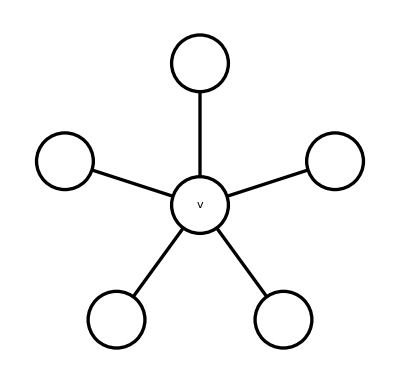

# Six-color Theorem for Planar Graphs, continued

Delete v and all edges incident with v and call the new graph G’. That is, G’ = G\v.

Zoom in on the neighbors of v.

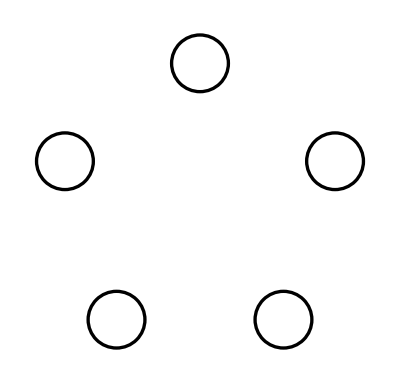

By the induction hypothesis, G’, which has n-1 vertices, can be properly colored with six or fewer colors.

Do so and call the colors 1,2,3,4,5,6.

Consider the (at most) five neighbors of v in G: WLOG they are v_1, v_2, …,v_5 and suppose WLOG that v_i has been colored with color i for i = 1,…,5.

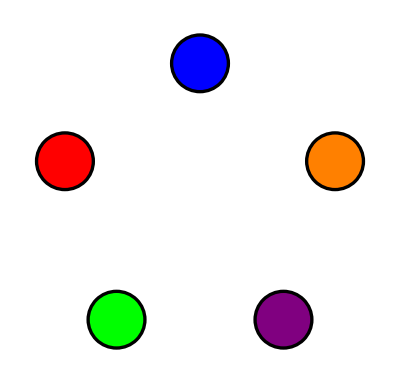

# Six-Color Theorem, continued

Return vertex v to G with its associated edges and now color 6 is available for v we are done.

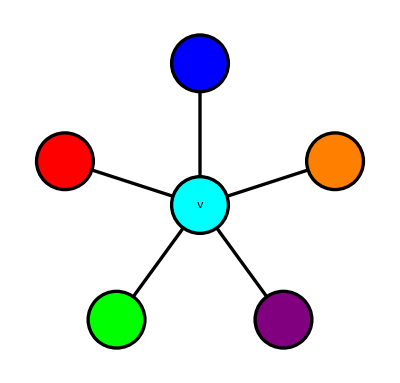

Note that if deg(v) < 5 a similar and even easier argument holds.

Thus by induction, if G is any planar graph, then χ(G) ≤ 6. QED

## The 5-Color Theorem for Planar Graphs

Next we’ll prove the 5-color theorem for planar graphs, but first we need a gadget called a “Kempe Chain.”

### Definition 6.2 [Kempe Chain]

Let G be a connected graph that has been properly vertex colored. Suppose c_1 and c_2 are two of the colors used in the vertex coloring of G. Let v ∈ V(G) be colored c_1.  Then the c_1c_2-Kempe Chain containing v is the maximal connected component of G that contains v and only vertices colored c_1 or c_2.

## Examples of Kempe Chains

## Kempe Chain Examples

1. Find the RB Kempe Chain containing vertex 7.
2. Find the RB Kempe Chain containing vertex 5.
3. Find the RB Kempe Chain containing vertex 6.
4. Find the YG Kempe Chain containing vertex 8.
5. Find the YG Kempe Chain containing vertex 2.
6. Find the RG Kempe Chain containing vertex 9.

## Kempe Chain Switch

### Definition 6.3. Let G be a properly colored graph and suppose K is a c_1c_2-Kempe chain containing vertex v_1 colored c_1. A c_1c_2-Kempe chain switch of K interchanges the colors c_1 and c_2 on the vertices of K.

Why we care...

### Proposition 6.4. A Kempe chain switch in a properly vertex-colored graph yields a properly vertex-colored graph.

Proof. Exercise.

## The Five Color Theorem

### Theorem 6.5 [The 5-color theorem for planar graphs]

Let G be a planar graph. Then χ(G) ≤ 5.

Proof.

Assume that all planar graphs with fewer than n vertices can be properly vertex-colored with five or fewer colors. What are your bases cases?

Re-run the proof of Theorem 6.3 up to the point where we examine the five neighbors of V.

Assume the five given colors are 1,2,3,4,5.

Case 1. If deg(V) < 5, then there will be a color left over from among 1,2,3,4,5 to use on V and we are done.

Case 2. If deg(V) = 5 but not all of the colors 1,2,3,4,5 are used on the neighbors of V, then there is a color left over to use on V.

Case 3. If deg(V) = 5 and vertex v_i is colored i for i = 1, …, 5, then there is work to be done.

## Five Color Theorem proof; case 3

Back at the ranch we have deg(V) = 5 and the neighbors of V are v_1, …,v_5 and are colored 1,2,3,4,5, respectively.

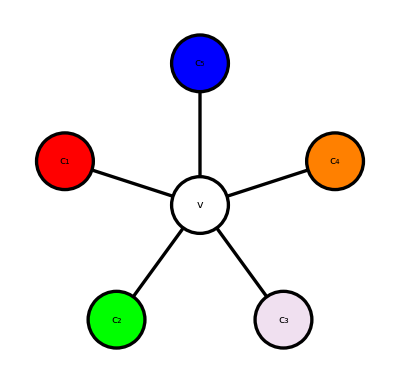

Subcase 3.1. Consider K = c_1c_3-Kempe chain containing v_1.

If K does not contain vertex v_3 then a c_1c_3-Kempe chain switch on K will leave c_1 available for V.

Subcase 3.2. Thus WLOG K contains both v_1 and v_3.

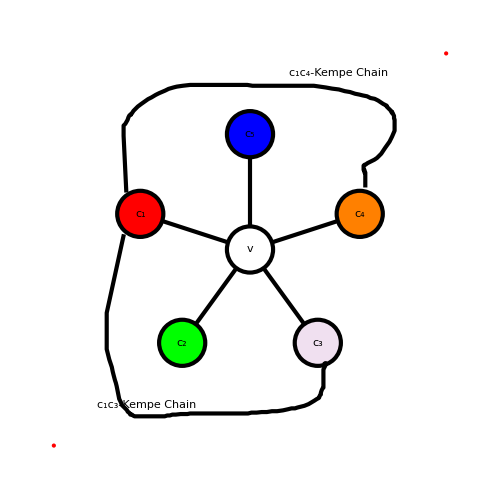

Then v_5 cannot be contained in J=c_2c_5-Kempe chain containing v_2 because K forms a c_1c_3 barrier.

In that case a c_2c_5-Kempe chain switch on J leaves c_2 available for V. Done

In all cases, we have inductively colored G with at most five colors and hence χ(G) ≤ 5. ▮

## Four Color Theorem

### Theorem 6.6 [The Four Color Theorem]

Let G be a simple planar graph. Then χ(G) ≤ 4 and the bound is sharp.

Proof.

Re-run the proofs of Theorems 6.3 and 6.5 up to the point where we examine a vertex V of degree 5 or less.

Case 1. If the neighbors of V are collectively colored with three or fewer colors then simply replace V and color it with a left over color and done.

Case 2. Assume deg(V) = 4 and the neighbors of V in the plane embedding of G\V are v_1, v_2, v_3, and v_4, colored R, G, B, and Y respectively.

As in Theorem 6.5, WLOG assume that  v_1 and v_3 are contained in the same RB-Kempe chain.

Then v_2 and v_4 cannot be contained in the same GY-Kempe chain and thus a GY-Kempe chain switch will leave a color available for V.

## Four Color Theorem, proof

Case 3. Assume deg(V) = 5 and WLOG all four colors are used on the neighbors of V.

Remark. Exactly one color will be used twice (on the neighbors of V)  in this scenario. Why?

Assume that color is G(reen).

Then either the two Gs are next to each other (RGGBY) or,

the two Gs are separated by one vertex (RGBGY). Why?

Subcase 3.1: The two Gs are next to each other v_1v_2 v_3 v_4 v_5 = RGGBY.

If the RB-Kempe chain containing v_1 does not contain v_4 then an RB-Kempe chain switch leaves color R available for V.

Thus WLOG v_1 and v_4 are on the same RB Kempe chain.

Then the YG-Kempe chain containing v_5 cannot contain either of v_2 or v_3.

Hence a YG-Kempe chain switch leaves color Y available for V. Done.

## Four Color Theorem, proof

Subcase 3.2: The two Gs are separated by one vertex v_1v_2 v_3 v_4 v_5=RGBGY.

WLOG there is an RB-Kempe chain that contains both v_1 and v_3 and

there is a YB-Kempe chain that contains both v_3 and v_5.

Morever, there is no GY-Kempe chain that includes both v_2 and v_5, and

there is no RG-Kempe chain that contains both v_1 and v_4 (because of the RB- and YB-Kempe chains above).

Perform both the YB- ad RB-Kempe chain switches, thus leaving color G available for V.

QED????????

Find the flaw in Kempe’s proof!